```mathematica
(*Mathematica*)
```

```mathematica
(*In this limiting singularity field model with symmetry of SO(3) to SU(3),
the quarks take on mass as they approach sinularity ( as quantum black holes)
and an electron is made up of three complex quarks.
The Schrödinger cat is both alive (has mass) and dead (is singular).*)
```

```mathematica
(* quark singularity limiting field*)
```

```mathematica
f[x_]=Sum[(a0*x)^i,{i,0,Infinity}]
```

1/(1-a0 x)

```mathematica
(* SO(3)-SU(3) field model: zero trace*)
```

```mathematica
Fvu={{0,f[x],-f[x]},{-f[x],0,f[x]},{f[x],-f[x],0}}
```

{{0,1/(1-a0 x),-1/(1-a0 x)},{-1/(1-a0 x),0,1/(1-a0 x)},{1/(1-a0 x),-1/(1-a0 x),0}}

```mathematica
p[x_]=CharacteristicPolynomial[Fvu,x]
```

-x^3-(3 x)/(1-a0 x)^2

```mathematica
ch=x/.Solve[p[x]==0,x]
```

{0,(1-√(1-4 ⅈ √3 a0))/(2 a0),(1+√(1-4 ⅈ √3 a0))/(2 a0),(1-√(1+4 ⅈ √3 a0))/(2 a0),(1+√(1+4 ⅈ √3 a0))/(2 a0)}

```mathematica
ch/.a0->1/x/.x->hbar^(1/3)/2/.hbar->1.054148*10^(-27)
```

{0,-0.0000209924+0.0000209926 ⅈ,0.0000209929-0.0000209926 ⅈ,-0.0000209924-0.0000209926 ⅈ,0.0000209929+0.0000209926 ⅈ}

```mathematica
(* centered square lattice*)
```

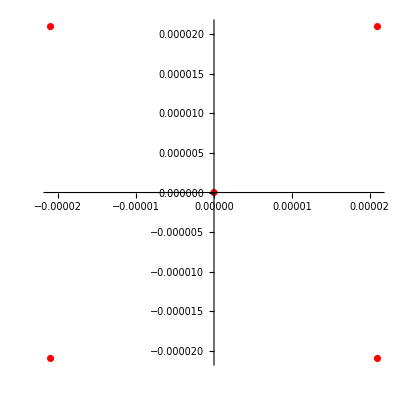

```mathematica
ComplexListPlot[{0,-0.000020992394817215496+0.000020992649248927303 ⅈ,0.000020992903683722872-0.000020992649248927303 ⅈ,-0.000020992394817215496-0.000020992649248927303 ⅈ,0.000020992903683722872+0.000020992649248927303 ⅈ},PlotStyle->Red]
```

```mathematica
Eigenvalues[Fvu]
```

{(ⅈ √3)/(-1+a0 x),-(ⅈ √3)/(-1+a0 x),0}

```mathematica
{(ⅈ √3)/(-1+a0 x),-(ⅈ √3)/(-1+a0 x),0}/.a0->1/x/.x->hbar^(1/3)/2/.hbar->1.054148*10^(-27)
```

Power::infy: Infinite expression 1/0 encountered.

{ComplexInfinity,ComplexInfinity,0}

```mathematica
Det[Fvu]
```

0

```mathematica
(*energy density matrix*)
```

```mathematica
Tvu=Fvu.Transpose[Fvu]/3
```

{{2/(3 (1-a0 x)^2),-1/(3 (1-a0 x)^2),-1/(3 (1-a0 x)^2)},{-1/(3 (1-a0 x)^2),2/(3 (1-a0 x)^2),-1/(3 (1-a0 x)^2)},{-1/(3 (1-a0 x)^2),-1/(3 (1-a0 x)^2),2/(3 (1-a0 x)^2)}}

```mathematica
Eigenvalues[Tvu]
```

```mathematica
{1/(-1+a0 x)^2,1/(-1+a0 x)^2,0}/.a0->1/x/.x->hbar^(1/3)/2/.hbar->1.054148*10^(-27)
```

Power::infy: Infinite expression 1/0^2 encountered.

{ComplexInfinity,ComplexInfinity,0}

```mathematica
(* seven Particle solution with zero mass cental*)
```

```mathematica
q[x_]=CharacteristicPolynomial[Tvu,x]
```

-x^3-x/(1-a0 x)^4+(2 x^2)/(1-a0 x)^2

```mathematica
qx=x/.Solve[q[x]==0,x]
```

{0,1/3 (2/a0+2^(1/3)/((-2 a0^3+27 a0^4+3 √3 √(-4 a0^7+27 a0^8))^(1/3))+((-2 a0^3+27 a0^4+3 √3 √(-4 a0^7+27 a0^8))^(1/3))/(2^(1/3) a0^2)),1/3 (2/a0+2^(1/3)/((-2 a0^3+27 a0^4+3 √3 √(-4 a0^7+27 a0^8))^(1/3))+((-2 a0^3+27 a0^4+3 √3 √(-4 a0^7+27 a0^8))^(1/3))/(2^(1/3) a0^2)),2/(3 a0)-(1+ⅈ √3)/(3 2^(2/3) (-2 a0^3+27 a0^4+3 √3 √(-4 a0^7+27 a0^8))^(1/3))-((1-ⅈ √3) (-2 a0^3+27 a0^4+3 √3 √(-4 a0^7+27 a0^8))^(1/3))/(6 2^(1/3) a0^2),2/(3 a0)-(1+ⅈ √3)/(3 2^(2/3) (-2 a0^3+27 a0^4+3 √3 √(-4 a0^7+27 a0^8))^(1/3))-((1-ⅈ √3) (-2 a0^3+27 a0^4+3 √3 √(-4 a0^7+27 a0^8))^(1/3))/(6 2^(1/3) a0^2),2/(3 a0)-(1-ⅈ √3)/(3 2^(2/3) (-2 a0^3+27 a0^4+3 √3 √(-4 a0^7+27 a0^8))^(1/3))-((1+ⅈ √3) (-2 a0^3+27 a0^4+3 √3 √(-4 a0^7+27 a0^8))^(1/3))/(6 2^(1/3) a0^2),2/(3 a0)-(1-ⅈ √3)/(3 2^(2/3) (-2 a0^3+27 a0^4+3 √3 √(-4 a0^7+27 a0^8))^(1/3))-((1+ⅈ √3) (-2 a0^3+27 a0^4+3 √3 √(-4 a0^7+27 a0^8))^(1/3))/(6 2^(1/3) a0^2)}

```mathematica
qx/.a0->1/x/.x->hbar^(1/3)/2/.hbar->1.054148*10^(-27)
```

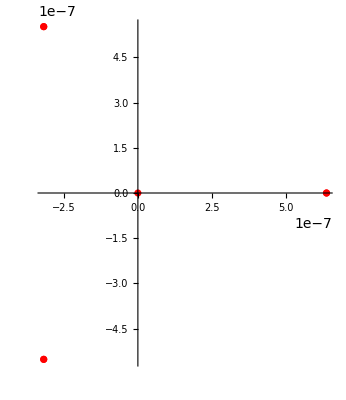

```mathematica
ComplexListPlot[{0,6.377253748309535*^-7,6.377253748309535*^-7,-3.183538209081029*^-7+5.519925028415751*^-7 ⅈ,-3.183538209081029*^-7+5.519925028415751*^-7 ⅈ,-3.183538209081029*^-7-5.519925028415751*^-7 ⅈ,-3.183538209081029*^-7-5.519925028415751*^-7 ⅈ},PlotStyle->Red]
```

```mathematica
(* 6+Pi over Alpha radius*)
```

```mathematica
(6.377253748309535*^-7)/(5.088665073738972*^-10)/137.03608/(6+Pi)
```

1.0004

```mathematica
Det[Tvu]
```

0

```mathematica
(* trace energy*)
```

```mathematica
ed=Tr[Tvu]
```

2/(1-a0 x)^2

```mathematica
(*wave particle duality energy density*)
```

```mathematica
ed1=m*c/(4*Pi*x^2/3)/.m->2*Pi*hbar/(x*c)
```

(3 hbar)/(2 x^3)

```mathematica
(* solving at the singularity radius*)
```

```mathematica
r=x/.Solve[ed==ed1,x]
```

{(a0^2 hbar)/4-(72 a0 hbar-9 a0^4 hbar^2)/(36 (24 hbar-12 a0^3 hbar^2+a0^6 hbar^3+8 √(9 hbar^2-a0^3 hbar^3))^(1/3))+1/4 (24 hbar-12 a0^3 hbar^2+a0^6 hbar^3+8 √(9 hbar^2-a0^3 hbar^3))^(1/3),(a0^2 hbar)/4+((1+ⅈ √3) (72 a0 hbar-9 a0^4 hbar^2))/(72 (24 hbar-12 a0^3 hbar^2+a0^6 hbar^3+8 √(9 hbar^2-a0^3 hbar^3))^(1/3))-1/8 (1-ⅈ √3) (24 hbar-12 a0^3 hbar^2+a0^6 hbar^3+8 √(9 hbar^2-a0^3 hbar^3))^(1/3),(a0^2 hbar)/4+((1-ⅈ √3) (72 a0 hbar-9 a0^4 hbar^2))/(72 (24 hbar-12 a0^3 hbar^2+a0^6 hbar^3+8 √(9 hbar^2-a0^3 hbar^3))^(1/3))-1/8 (1+ⅈ √3) (24 hbar-12 a0^3 hbar^2+a0^6 hbar^3+8 √(9 hbar^2-a0^3 hbar^3))^(1/3)}

```mathematica
rx=r/.a0->1/x
```

{1/4 (24 hbar+8 √(9 hbar^2-hbar^3/x^3)+hbar^3/x^6-(12 hbar^2)/x^3)^(1/3)-(-(9 hbar^2)/x^4+(72 hbar)/x)/(36 (24 hbar+8 √(9 hbar^2-hbar^3/x^3)+hbar^3/x^6-(12 hbar^2)/x^3)^(1/3))+hbar/(4 x^2),-1/8 (1-ⅈ √3) (24 hbar+8 √(9 hbar^2-hbar^3/x^3)+hbar^3/x^6-(12 hbar^2)/x^3)^(1/3)+((1+ⅈ √3) (-(9 hbar^2)/x^4+(72 hbar)/x))/(72 (24 hbar+8 √(9 hbar^2-hbar^3/x^3)+hbar^3/x^6-(12 hbar^2)/x^3)^(1/3))+hbar/(4 x^2),-1/8 (1+ⅈ √3) (24 hbar+8 √(9 hbar^2-hbar^3/x^3)+hbar^3/x^6-(12 hbar^2)/x^3)^(1/3)+((1-ⅈ √3) (-(9 hbar^2)/x^4+(72 hbar)/x))/(72 (24 hbar+8 √(9 hbar^2-hbar^3/x^3)+hbar^3/x^6-(12 hbar^2)/x^3)^(1/3))+hbar/(4 x^2)}

```mathematica
(*radius three particles:3 quarks*)
```

```mathematica
Union[Flatten[Table[x/.Solve[rx[[i]]==x,x],{i,3}]]]
```

```mathematica
FullSimplify[Apply[Plus,Abs[{hbar^(1/3)/2,-1/2 (-1)^(1/3) hbar^(1/3),1/2 (-1)^(2/3) hbar^(1/3)}]/3]]
```

1/2 Abs[hbar]^(1/3)

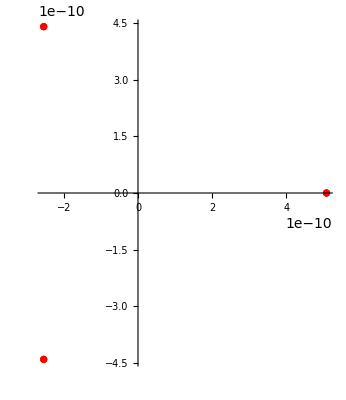

```mathematica
ComplexListPlot[Flatten[Table[x/.Solve[rx[[i]]==x,x],{i,3}]]/.hbar->1.054148*10^(-27),PlotStyle->Red]
```

```mathematica
x0=Union[Flatten[Table[x/.Solve[rx[[i]]==x,x],{i,3}]]]/.hbar->1.054148*10^(-27)
```

{5.08867×10^-10,-2.54433×10^-10-4.40691×10^-10 ⅈ,-2.54433×10^-10+4.40691×10^-10 ⅈ}

```mathematica
(*total Sphere volume mass*)
```

```mathematica
vm=Table[(4*Pi/3)*x0[[i]]^3,{i,3}]/(9.109558*10^(-28))
```

{0.605903,0.605903-2.06192×10^-16 ⅈ,0.605903-5.1548×10^-16 ⅈ}

```mathematica
Abs[vm]
```

{0.605903,0.605903,0.605903}

```mathematica
Apply[Plus,{0.6059027255761448,0.6059027255761448-2.061920556442718*^-16 ⅈ,0.6059027255761451-5.154801391106795*^-16 ⅈ}]
```

1.81771-7.21672×10^-16 ⅈ

```mathematica
(* radial polynomial*)
```

```mathematica
ExpandAll[Product[x-x0[[i]],{i,3}]]
```

(-1.31769×10^-28+5.60519×10^-44 ⅈ)+(2.40741×10^-35+0. ⅈ) x-(5.16988×10^-26+1.55096×10^-25 ⅈ) x^2+x^3

```mathematica
(*Particle-wave duality masses*)
```

```mathematica
m0=Table[2*Pi*hbar/(x0[[i]]*c),{i,3}]/.hbar->1.054148*10^(-27)/. c->2.997923*10^10
```

{4.34167×10^-28,-2.17084×10^-28+3.76×10^-28 ⅈ,-2.17084×10^-28-3.76×10^-28 ⅈ}

```mathematica
pm=m0/(9.109558*10^(-28))
```

{0.476606,-0.238303+0.412753 ⅈ,-0.238303-0.412753 ⅈ}

```mathematica
Abs[pm]
```

{0.476606,0.476606,0.476606}

```mathematica
(*total wave particle singularity mass*)
```

```mathematica
Apply[Plus,m0/(9.109558*10^(-28))]//Chop
```

0

```mathematica
(*mass polynomial*)
```

```mathematica
FullSimplify[ExpandAll[Product[x-m0[[i]],{i,3}]]]
```

(-8.18411×10^-83-4.38907×10^-98 ⅈ)+x (3.62227×10^-71+((-1.34525×10^-43+1.79366×10^-43 ⅈ)+x) x)

```mathematica
(*average total massses*)
```

```mathematica
Apply[Plus,Table[(vm[[i]]+pm[[i]])/2,{i,3}]]
```

0.908854-4.44089×10^-16 ⅈ

```mathematica
(*geoaverage*)
```

```mathematica
Apply[Plus,Table[Sqrt[(vm[[i]]*pm[[i]])],{i,3}]]
```

1.07476-3.33067×10^-16 ⅈ

```mathematica
(*end*)
```